## Preamble

```mathematica
LaunchKernels[8];
<< KerrGeodesics`
<< GeneralRelativityTensors`
<<SpinWeightedSpheroidalHarmonics`
<<Teukolsky`
ParallelNeeds["SpinWeightedSpheroidalHarmonics`"];
ParallelNeeds["Teukolsky`"];
ParallelNeeds["KerrGeodesics`"];
Information[PacletObject["Teukolsky"]]
```

Paclet

```mathematica
setup[e_,p_,a_]:=Module[{g,Σ,Δ,subs,rdotsqr,ω, Tradmino, integrand, rdot, const, Ε,L, ul,um,Ω,Trad, orbit, t0,r0,θ0,ϕ0,Q0,K0, Δ0, A,B, ℭ, χ, Wr,prec =32},
(*calculate tensor quantities*)
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 M r + a^2;

(*calculate orbit quantities*)
const = KerrGeoConstantsOfMotion[a,p,e,1];
Ε=const[[1]];
L=const[[2]];

Ω= KerrGeoFrequencies[a,p,e,1];
Trad =2π/Ω[[1]];
Tradmino=2π/KerrGeoFrequencies[a,p,e,1,Time->"Mino"][[1]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],SetPrecision[1,prec]];

(**)
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
rdot[λ_]:= r0'[λ]/r0[λ]^2;

ul[s_,λ_] :=(r^2 rdot[λ] -s (r^2+a^2)Ε +s  a  L)/Δ;
um[s_]:=s ⅈ(L-a Ε);

(*seup definitions for calculations*)
ω[m_,n_]:=m Ω[[3]] + n Ω[[1]];
Q0[m_,n_] := m-a ω[m,n];
K0[m_,n_,λ_]:= ω[m,n](r0[λ]^2 + a^2)- a m;
Δ0[λ_] := Δ/.{r->r0[λ],M->1};
A[s_,m_,n_,λ_]:=ul[s,λ](-s Q0[m,n] + ⅈ a/r0[λ]) - um[s] (- s ⅈ K0[m,n,λ]/Δ0[λ]+1/r0[λ])/.{r->r0[λ],θ->π/2,M->1};
B[s_,λ_]:= -ul[s,λ]/.{r->r0[λ],θ->π/2,M->1};
ℭ[s_,λ_]:=-um[s]/.{r->r0[λ],θ->π/2,M->1};

(*write our integrand*)
χ[s_,l_,m_,n_,λ_,R_]:=Module[{Ph,Phd,Pinf, Pinfd},
(*define W *)
Ph= Piecewise[{{1,s==-1},{Δ0[λ],s==1}}] R["In"][r0[λ]];
Phd= Piecewise[{{R["In"]'[r0[λ]],s==-1},{Δ0[λ] R["In"]'[r0[λ]] + R["In"][r0[λ]](-2+2 r0[λ]),s==1}}];
Pinf :=  Piecewise[{{1,s==-1},{Δ0[λ],s==1}}] R["Up"][r0[λ]];
Pinfd:=  Piecewise[{{R["Up"]'[r0[λ]],s==-1},{Δ0[λ] R["Up"]'[r0[λ]] + R["Up"][r0[λ]](-2+2 r0[λ]),s==1}}];
(*Calculate integrand*)
If[Floor[s]==-1,
(A[s,m,n,λ]SpinWeightedSpheroidalHarmonicS[s,l,m,a ω[m,n],π/2,0] + B[s,λ]ReplaceAll[θ->π/2][D[SpinWeightedSpheroidalHarmonicS[s,l,m,a ω[m,n],θ,0],θ]] )Ph -Phd SpinWeightedSpheroidalHarmonicS[s,l,m,a ω[m,n],π/2,0]  ℭ[s,λ],
(A[s,m,n,λ]SpinWeightedSpheroidalHarmonicS[s,l,m,a ω[m,n],π/2,0] + B[s,λ]ReplaceAll[θ->π/2][D[SpinWeightedSpheroidalHarmonicS[s,l,m,a ω[m,n],θ,0],θ]] )Pinf -Pinfd SpinWeightedSpheroidalHarmonicS[s,l,m,a ω[m,n],π/2,0]  ℭ[s,λ]]
];
Wr[s_,λ_,R_]:=Module[{Ph,Phd,Pinf, Pinfd},
Ph= Piecewise[{{1,s==-1},{Δ0[λ],s==1}}] R["In"][r0[λ]];
Phd= Piecewise[{{R["In"]'[r0[λ]],s==-1},{Δ0[λ] R["In"]'[r0[λ]] + R["In"][r0[λ]](-2+2 r0[λ]),s==1}}];
Pinf :=  Piecewise[{{1,s==-1},{Δ0[λ],s==1}}] R["Up"][r0[λ]];
Pinfd:=  Piecewise[{{R["Up"]'[r0[λ]],s==-1},{Δ0[λ] R["Up"]'[r0[λ]] + R["Up"][r0[λ]](-2+2 r0[λ]),s==1}}];
Ph Pinfd - Pinf Phd
];
integrand[s_,l_,m_,n_,λ_,R_]:=r0[λ] Exp[ⅈ(ω[m,n]t0[λ] -m ϕ0[λ])] χ[s,l,m,n,λ,R]/Wr[s,λ,R];
α[s_,l_,m_,n_]:=(4π q)1/(Trad Sqrt[2])Module[{R,y,λ1,rmin,rmax},
rmin = orbit["p"]/(1+orbit["e"]+0.1);
            rmax = orbit["p"]/(1-orbit["e"]-0.1);
R = TeukolskyRadial[s, l, m, a, ω[m,n], Method->{"NumericalIntegration","Domain"-> {"In"->{rmin,rmax}, "Up"->{rmin,rmax}}}];
y = NDSolve[{f'[λ1] == integrand[s,l,m,n,λ1,R],f[0]==0},f,{λ1,0,Tradmino},AccuracyGoal->10,PrecisionGoal->10];
(f[Tradmino]/.y)[[1]]
];
]
```

## Calculating ϕ_1

## Calculating homogenous Φ_1 given a radius r

```mathematica
ϕ1[a_,p_,e_, l_,m_,n_]:=Module[{Ω,ω, Σ, Δ, Trad, Tradmino, orbit, t0,r0,θ0, ϕ0, Q0,K0,Β, λ, prec=32},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,1];
ω=m Ω[[3]] + n Ω[[1]];
Trad =2π/Ω[[1]];
Tradmino=2π/KerrGeoFrequencies[a,p,e,1,Time->"Mino"][[1]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],SetPrecision[1,prec]];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
Q0 := m-a ω[m,n];
K0[λ_]:= ω[m,n](r0[λ]^2 + a^2)- a m;
λ = SpinWeightedSpheroidalEigenvalue[1,l,m,a ω];
Β= Sqrt[λ^2+ 4 a m ω - 4 a^2 ω^2];
(*To Do: calculate g_(+1) and Subscript[f, -1] and then combine them to calculate Subscript[ϕ, 1]*)
]
```

## Calculating ϕ_0 and ϕ_2

```mathematica
OrbitTP[p_,e_]:= Module[{},{rMax, rMin}/.NSolve[{p== (2 rMax rMin)/(rMax + rMin), e == (rMax-rMin)/(rMax + rMin)}, {rMax, rMin}][[1]]
]
```

```mathematica
LMAX = 2;NMAX=2;
```

```mathematica
Φ0 [a_ , r_ ,τmino_, p_,e_]:= Module[{Δ,Ω,orbit, rmin, rmax,sum,t0,r0,θ0,ϕ0, M=1,prec= 32},
Δ=r^2-2 M r + a^2;
Ω= KerrGeoFrequencies[a,p,e,SetPrecision[1,prec]];
orbit = KerrGeoOrbit[SetPrecision[a,prec],SetPrecision[p,prec],SetPrecision[e,prec],1];
{t0,r0,θ0,ϕ0}=orbit["Trajectory"];
{rmax,rmin} =OrbitTP[p,e];
If[r>= rmax,
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["Up"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℐ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{l,1,LMAX},{m,-l,l},{n,1,NMAX}
];
];
If[r<= rmin,
sum =Table[
Module[{α,ω,P,S,R,expFactor},
ω= m Ω[[3]] + n Ω[[1]];
R = TeukolskyRadial[1,l,m,a, ω];
P=R["In"][r]Δ;
α = TeukolskyPointParticleMode[1 , l,m,n,0,orbit]["Amplitudes"]["ℋ"]; 
S=SpinWeightedSpheroidalHarmonicS[1,l,m,a ω][θ0[τmino], ϕ0[τmino]];
expFactor = Exp[-ⅈ ω t0[τmino] + ⅈ m ϕ0[τmino]];
S expFactor α P
]
,{l,1,LMAX},{m,-l,l},{n,1,NMAX}
];
];
Δ^-1 Total[Flatten[sum]]
]
```

```mathematica
AbsoluteTiming[Φ0 [0 , lowerRs[[1]],0.5,10,0.1]]
```

{11.9242,-0.000797937+0.00114182 ⅈ}

```mathematica
Module[{rmin, rmax,a=0, p=10,e=0.1, τmino=0.5},
{rmax, rmin} = OrbitTP[p,e];
lowerRs =Subdivide[KerrGeoSeparatrix[a,e,1], rmin, 50];
upperRs = Subdivide[rmax, 20,50];
Print[lowerRs[[1]]];
lowerΦ0 = ParallelTable[Φ0 [a , lowerRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}];
upperΦ0 =ParallelTable[Φ0 [a , upperRs[[i]] ,τmino, p,e],{i,1 ,Length[lowerRs]}];
]
```

6.2

```mathematica
{rmax, rmin} = OrbitTP[10,0.1];
```

```mathematica
AllData = Flatten[{Re[lowerΦ0],Im[lowerΦ0], Re[upperΦ0],Im[upperΦ0]}]
lineStyle={Thick,Black,Dashed};
line1=Line[{{rmin,Min[AllData]},{rmin,Max[AllData]}}];
line2=Line[{{rmax,Min[AllData]},{rmax,Max[AllData]}}];
```

{-0.000797937,-0.000807829,-0.000817684,-0.0008275,-0.000837278,-0.000847018,-0.00085672,-0.000866385,-0.000876013,-0.000885603,-0.000895156,-0.000904672,-0.00091415,-0.000923592,-0.000932997,-0.000942364,-0.000951695,-0.000960989,-0.000970246,-0.000979466,-0.00098865,-0.000997796,-0.00100691,-0.00101598,-0.00102501,-0.00103401,-0.00104297,-0.0010519,-0.00106079,-0.00106964,-0.00107845,-0.00108723,-0.00109597,-0.00110467,-0.00111333,-0.00112196,-0.00113055,-0.0011391,-0.00114761,-0.00115609,-0.00116453,-0.00117293,-0.00118129,-0.00118962,-0.00119791,-0.00120615,-0.00121437,-0.00122254,-0.00123067,-0.00123877,-0.00124682,0.00114182,0.00114964,0.00115749,0.00116537,0.00117329,0.00118124,0.00118923,0.00119724,0.00120529,0.00121338,0.00122149,0.00122964,0.00123782,0.00124604,0.00125428,0.00126256,0.00127087,0.00127921,0.00128759,0.00129599,0.00130443,0.0013129,0.0013214,0.00132993,0.00133849,0.00134708,0.0013557,0.00136436,0.00137304,0.00138175,0.0013905,0.00139927,0.00140807,0.0014169,0.00142576,0.00143465,0.00144357,0.00145252,0.00146149,0.0014705,0.00147953,0.00148859,0.00149768,0.00150679,0.00151593,0.0015251,0.0015343,0.00154352,0.00155277,0.00156204,0.00157134,-0.000301905,-0.000287256,-0.00027353,-0.000260653,-0.00024856,-0.000237191,-0.000226492,-0.000216413,-0.000206909,-0.00019794,-0.000189466,-0.000181455,-0.000173873,-0.000166693,-0.000159888,-0.000153432,-0.000147304,-0.000141483,-0.000135949,-0.000130684,-0.000125672,-0.000120898,-0.000116348,-0.000112008,-0.000107866,-0.000103911,-0.000100132,-0.0000965203,-0.0000930654,-0.0000897592,-0.0000865936,-0.0000835613,-0.0000806551,-0.0000778686,-0.0000751956,-0.0000726302,-0.0000701672,-0.0000678014,-0.000065528,-0.0000633426,-0.0000612409,-0.000059219,-0.0000572731,-0.0000553996,-0.0000535953,-0.000051857,-0.0000501817,-0.0000485665,-0.000047009,-0.0000455064,-0.0000440565,0.00113322,0.00105294,0.000979468,0.000912131,0.000850325,0.000793518,0.000741235,0.000693054,0.000648597,0.000607527,0.000569541,0.000534368,0.000501764,0.000471509,0.000443405,0.000417273,0.00039295,0.000370291,0.000349162,0.000329443,0.000311023,0.000293802,0.00027769,0.000262603,0.000248465,0.000235207,0.000222764,0.000211078,0.000200097,0.000189769,0.000180051,0.000170901,0.000162279,0.000154151,0.000146484,0.000139247,0.000132414,0.000125957,0.000119852,0.000114079,0.000108615,0.000103443,0.0000985433,0.0000939003,0.0000894986,0.0000853237,0.0000813623,0.000077602,0.0000740311,0.0000706387,0.0000674147}

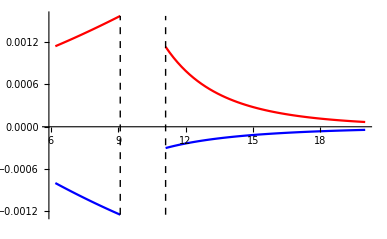

```mathematica
ListPlot[{Table[{lowerRs[[i]], Re[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{lowerRs[[i]], Im[lowerΦ0[[i]]]},{i, 1 Length[lowerRs]}],Table[{upperRs[[i]], Re[upperΦ0[[i]]]},{i, 1 Length[upperRs]}],Table[{upperRs[[i]], Im[upperΦ0[[i]]]},{i, 1 Length[upperRs]}] }, Joined->True, PlotStyle->{Blue, Red,Blue,Red},
Epilog->{Directive[lineStyle],line1,line2}
]
```

```mathematica
rmin
```

9.09091